```mathematica
m35=2 Γ d c(1+Cos[μ/2])(2wb/(wb^2-ws^2))/(μ);
m45=2 Γ d c^2(1+Cos[μ/2])(2wb/(wb^2-ws^2))/(μ wb);
M1=({{Cos[μ/2], Sin[μ/2], 0, 0, 0, 0}, {-Sin[μ/2], Cos[μ/2], 0, 0, 0, 0}, {Γ Sin[μ/2], Γ(2/μ Sin[μ/2]-Cos[μ/2]), Cos[μ/2], Sin[μ/2], m35, 0}, {Γ(2/μ Sin[μ/2]+Cos[μ/2]), Γ Sin[μ/2], -Sin[μ/2], Cos[μ/2], m45, 0}, {0, 0, 0, 0, -1, 0}, {0, 0, 0, 0, 0, 1}});
M2=({{Cos[μ/2], Sin[μ/2], Γ Sin[μ/2], Γ(2/μ Sin[μ/2]-Cos[μ/2]), m35, 0}, {-Sin[μ/2], Cos[μ/2], Γ(2/μ Sin[μ/2]+Cos[μ/2]), Γ Sin[μ/2], m45, 0}, {0, 0, Cos[μ/2], Sin[μ/2], 0, 0}, {0, 0, -Sin[μ/2], Cos[μ/2], 0, 0}, {0, 0, 0, 0, -1, 0}, {0, 0, 0, 0, 0, 1}});
M=Simplify[M1.M2];
```

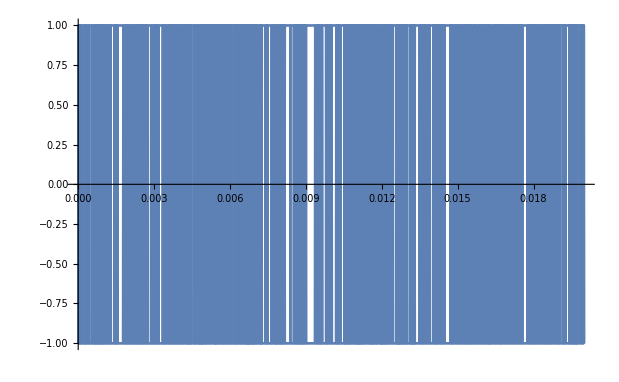

```mathematica
Plot[Re[Eigenvalues[M/.{wb->0.18,ws->0.04,μ->2π 0.18/0.04}]],{Γ,0,2}]
```

```mathematica
M1=({{Cos[μ/2], Sin[μ/2], 0, 0}, {-Sin[μ/2], Cos[μ/2], 0, 0}, {Γ Sin[μ/2], Γ(2/μ Sin[μ/2]-Cos[μ/2]), Cos[μ/2], Sin[μ/2]}, {Γ(2/μ Sin[μ/2]+Cos[μ/2]), Γ Sin[μ/2], -Sin[μ/2], Cos[μ/2]}});
M2=({{Cos[μ/2], Sin[μ/2], Γ Sin[μ/2], Γ(2/μ Sin[μ/2]-Cos[μ/2])}, {-Sin[μ/2], Cos[μ/2], Γ(2/μ Sin[μ/2]+Cos[μ/2]), Γ Sin[μ/2]}, {0, 0, Cos[μ/2], Sin[μ/2]}, {0, 0, -Sin[μ/2], Cos[μ/2]}});
M=Simplify[M1.M2];
```

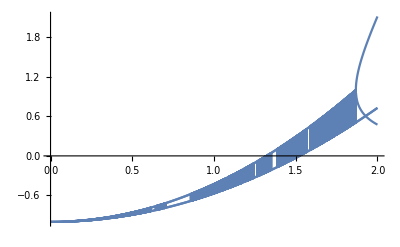

```mathematica
Plot[Re[Eigenvalues[M/.{wb->0.18,ws->0.4,μ->2π 0.18/0.04}]],{Γ,0,2}]
```